```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]];
```

Analytics

```mathematica
z0[β_,ω_,d_]:=(1/(2 Sinh[(β ℏ ω)/2]))^d/.{ℏ-> 1,m-> 1};
z[N_,β_,ω_,d_]:=If[N==0,1,1/N Sum[(-1)^(n-1)z0[n β,ω,d]z[N-n,β,ω,d],{n,1,N}]];
e[N_,β_,ω_,d_]:=-1/z[N,β,ω,d]D[z[N,β,ω,d],β];
```

```mathematica
z1=z[1,β,ω,d];
z2=z[2,β,ω,d];
```

```mathematica
Ω=2 z2/z1^2
```

2^(2 d) Csch[(β ω)/2]^(-2 d) (2^(-2 d) Csch[(β ω)/2]^(2 d)-2^-d Csch[β ω]^d)

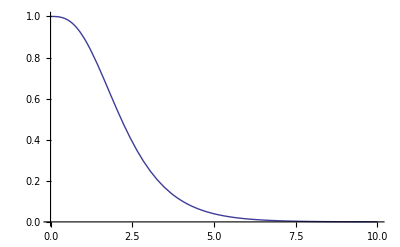

```mathematica
Plot[Ω/.{ω-> 1,d->3},{β,0,10}]
```

```mathematica
Clear[Ω]
```

```mathematica
e1=e[1,β,ω,d];
e2=FullSimplify[e[2,β,ω,d]];
ediff=FullSimplify[2e1-e2];
```

```mathematica
foo=DSolve[{Ω'[β]-(ediff/.{ω->1,d-> 3}) Ω[β]==0,Ω[0]==1},Ω[β],β]
```

{{Ω[β]→1/2 ⅇ^(-β/2) Sech[β/2]^3 (2 Cosh[β]+Sinh[β])}}

```mathematica
Ω=(Ω[β]/.foo)[[1]];
```

```mathematica
Plot[Ω,{β,0,10}]
```

-Graphics-

```mathematica
Clear[Ω]
```

Numerical Integration Methods

```mathematica
euler[f_,{x_,x0_,xn_},{y_,y0_},steps_]:=Block[{xold=x0,yold=y0,sollist={{x0,y0}},x,y,h},h=N[(xn-x0)/steps];
Do[xnew=xold+h;
ynew=yold+h*(f/.{x->xold,y->yold});
sollist=Append[sollist,{xnew,ynew}];
xold=xnew;
yold=ynew,{steps}];
Return[sollist]]
```

```mathematica
heun[f_,{x_,x0_,xn_},{y_,y0_},steps_]:=Block[{xold=x0,yold=y0,sollist={{x0,y0}},x,y,h},h=N[(xn-x0)/steps];
Do[xnew=xold+h;
slopeold=f/.{x->xold,y->yold};
slopenew=f/.{x->(xold+h),y->(yold+h*(f/.{x->xold,y->yold}))};
ynew=yold+0.5*h*(slopeold+slopenew);
sollist=Append[sollist,{xnew,ynew}];
xold=xnew;
yold=ynew,{steps}];
Return[sollist]]
```

```mathematica
RKA[f_,{x_,x0_,xn_},{y_,y0_},steps_]:=Block[{xold=x0,yold=y0,sollist={{x0,y0}},x,y,h},h=N[(xn-x0)/steps];
Do[xnew=xold+h;
k1=h*f/.{x->xold,y->yold};
k2=h*f/.{x->(xold+0.5*h),y->(yold+0.5*k1)};
k3=h*f/.{x->(xold+0.5*h),y->(yold+0.5*k2)};
k4=h*f/.{x->(xold+h),y->(yold+k3)};
ynew=yold+(1.0/6.0)*(k1+2k2+2k3+k4);
sollist=Append[sollist,{xnew,ynew}];
xold=xnew;
yold=ynew,{steps}];
Return[sollist]]
```

Discretized Analyic Results

```mathematica
β0=0.01;
βN=10.0;
Ω0=1.0;
nsteps=100;
f[β_,Ω_]:=(ediff/.{ω->1,d-> 3}) Ω
sol[β_]:=2 z2/z1^2/.{ω->1,d-> 3}
```

```mathematica
eulersol=euler[f[β,Ω],{β,β0,βN},{Ω,Ω0},nsteps];
heunsol=heun[f[β,Ω],{β,β0,βN},{Ω,Ω0},nsteps];
RKAsol=RKA[f[β,Ω],{β,β0,βN},{Ω,Ω0},nsteps];
```

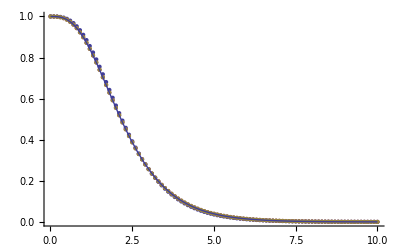

```mathematica
foo=ListPlot[{eulersol,heunsol,RKAsol}];
bar=Plot[sol[β],{β,β0,βN}];
Show[foo,bar]
```

```mathematica
npts=100;
dβ=(βN-β0)/(npts-1);
```

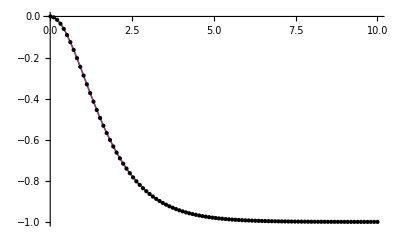

```mathematica
ediffpts=Table[{β,(ediff/.{ω-> 1,d-> 3})},{β,β0,βN,dβ}];
ediffint=Interpolation[ediffpts];
Plot[{ediffint[β],ediff/.{ω-> 1,d-> 3}},{β,β0,βN},Epilog->Map[Point,{ediffpts}]]
```

```mathematica
f[β_,Ω_]:=ediffint[β] Ω
```

```mathematica
eulersol=euler[f[β,Ω],{β,β0,βN},{Ω,Ω0},nsteps];
heunsol=heun[f[β,Ω],{β,β0,βN},{Ω,Ω0},nsteps];
RKAsol=RKA[f[β,Ω],{β,β0,βN},{Ω,Ω0},nsteps];
```

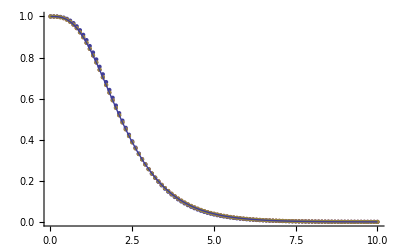

```mathematica
foo=ListPlot[{eulersol,heunsol,RKAsol}];
bar=Plot[sol[β],{β,β0,βN}];
Show[foo,bar]
```

```mathematica
npart=2;
nd=3;
nperm=1;
β0=0.1;
βN=10.0;
nbead=128;
beadexp=Log[2,nbead];
```

```mathematica
edata=Import[StringJoin["Fermions/epoints",ToString[npart],"-",ToString[nd],"-",ToString[2^beadexp],".dat"]];
```

{{0.1,61.02},{0.2,28.5274},{0.3,19.3528},{0.4,13.9295},{0.5,11.5247},{0.6,9.52185},{0.7,8.46957},{0.8,7.17224},{0.9,6.81957},{1,6.37422},{2,4.39254},{3,3.97801},{4,3.93074},{5,3.90504},{6,3.90403},{7,3.87798},{8,3.84321},{9,3.81392},{10,3.80732}}

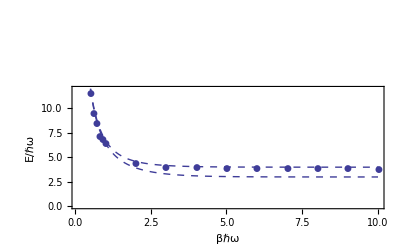

```mathematica
modelePlot=Plot[{e2,2*e1}/.{ω-> 1,d-> nd},{β,β0,βN},PlotRange-> {0,12},PlotStyle->Dashed];
permPlot=ListPlot[edata,PlotStyle->Thick,PlotMarkers-> Automatic];
Show[modelePlot,permPlot,LabelStyle->Directive[FontFamily->"Helvetica"],RotateLabel-> False,Frame->True,FrameLabel-> {Style["βℏω",Bold],Style["E/ℏω",Bold]}]
```

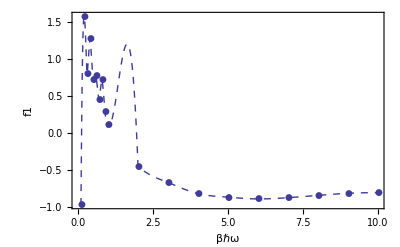

```mathematica
f1pts=Table[{edata[[i,1]],2(e1/.{β-> edata[[i,1]],ω->1,d->nd})-edata[[i,2]]},{i,1,Length[edata]}];
f1=Interpolation[f1pts];
f1ptsPlot=ListPlot[f1pts,PlotStyle->Thick,PlotMarkers-> Automatic,AxesOrigin->{0,0}];
f1Plot=Plot[f1[β],{β,β0,βN},PlotStyle->Dashed,AxesOrigin->{0,0}];
Show[f1Plot,f1ptsPlot,LabelStyle->Directive[FontFamily->"Helvetica"],RotateLabel-> False,Frame->True,FrameLabel-> {Style["βℏω",Bold],Style["f1",Bold]}]
```

```mathematica
f[β_,Ω_]:=f1[β] Ω
nsteps=100;
β0=0.1;
βN=10.0;
Ω0=1.0;
```

```mathematica
eulersol=euler[f[β,Ω],{β,β0,βN},{Ω,Ω0},nsteps];
heunsol=heun[f[β,Ω],{β,β0,βN},{Ω,Ω0},nsteps];
RKAsol=RKA[f[β,Ω],{β,β0,βN},{Ω,Ω0},nsteps];
```

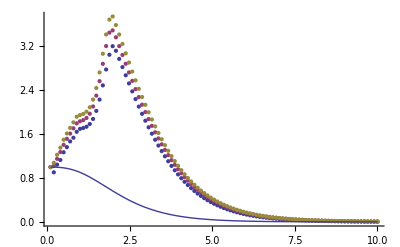

```mathematica
foo=ListPlot[{eulersol,heunsol,RKAsol}];
bar=Plot[sol[β],{β,β0,βN}];
Show[foo,bar]
```

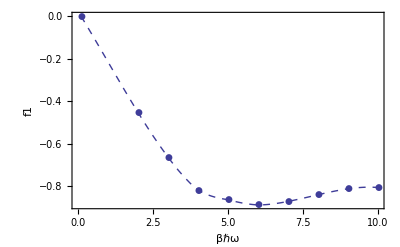

```mathematica
f1pts={{0.1,0.0},{2,-0.45343414350200595},{3,-0.663635821052464},{4,-0.8187958378173557},{5,-0.8643380705621753},{6,-0.8891205300589324},{7,-0.8725037144806698},{8,-0.8411965487949526},{9,-0.813179449784323},{10,-0.8070475880539418}};
f1=Interpolation[f1pts];
f1ptsPlot=ListPlot[f1pts,PlotStyle->Thick,PlotMarkers-> Automatic,AxesOrigin->{0,0}];
f1Plot=Plot[f1[β],{β,β0,βN},PlotStyle->Dashed,AxesOrigin->{0,0}];
Show[f1Plot,f1ptsPlot,LabelStyle->Directive[FontFamily->"Helvetica"],RotateLabel-> False,Frame->True,FrameLabel-> {Style["βℏω",Bold],Style["f1",Bold]}]
```

```mathematica
f[β_,Ω_]:=f1[β] Ω
nsteps=100;
β0=0.1;
βN=10.0;
Ω0=1.0;
```

```mathematica
eulersol=euler[f[β,Ω],{β,β0,βN},{Ω,Ω0},nsteps];
heunsol=heun[f[β,Ω],{β,β0,βN},{Ω,Ω0},nsteps];
RKAsol=RKA[f[β,Ω],{β,β0,βN},{Ω,Ω0},nsteps];
```

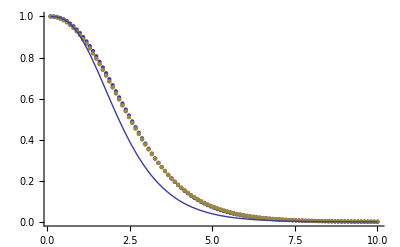

```mathematica
foo=ListPlot[{eulersol,heunsol,RKAsol}];
bar=Plot[sol[β],{β,β0,βN}];
Show[foo,bar]
```

```mathematica
Omega=Interpolation[RKAsol];
```

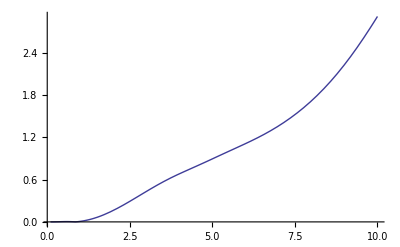

```mathematica
Plot[Abs[(z2/.{ω-> 1,d-> 3})-(1/2 Omega[β] z1^2/.{ω-> 1,d-> 3})]/(z2/.{ω-> 1,d-> 3}),{β,0.1,10}]
```

```mathematica
nsol1=NDSolve[{y'[t]==f1[t]y[t],y[0.1]==1.0},y,{t,0.1,10}];
```

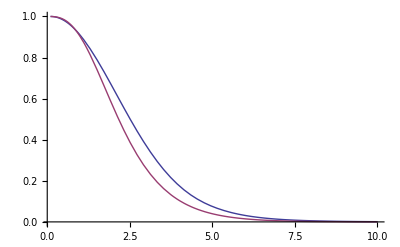

```mathematica
Plot[{y[β]/.nsol1,sol[β]},{β,0.1,10},PlotRange-> {0.0,1.0}]
```

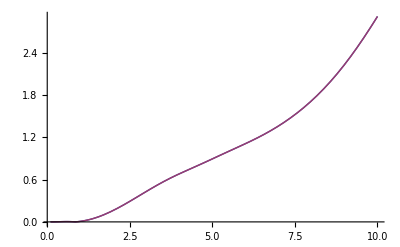

```mathematica
Plot[{Abs[(z2/.{ω-> 1,d-> 3})-(1/2 Omega[β] z1^2/.{ω-> 1,d-> 3})]/(z2/.{ω-> 1,d-> 3}),Abs[(z2/.{ω-> 1,d-> 3})-(1/2(y[β]/.nsol1)(z1^2/.{ω-> 1,d-> 3}))]/(z2/.{ω-> 1,d-> 3})},{β,0.1,10}]
```